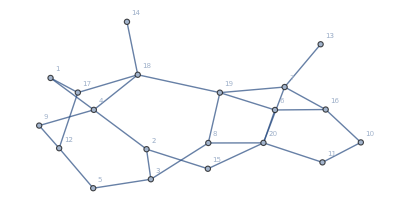

Обход в глубину:{8,3,2,4,1,17,12,5,9,18,14,19,6,16,7,13,20,11,10,15}

```mathematica
(*РАСЧЕТ МАТРИЦЫ РАССТОЯНИЙ (Агоритм Флойда)*)
Unprotect[D];
(*Матрица смежности*)
D={
{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0}
};

vertexCount=Length[D];
G=UndirectedGraph[AdjacencyGraph[D],VertexLabels->Table[i->Subscript["",i],{i,vertexCount}]];

GetAdjacencyList[v_]:=
(
adjacencyList={};
For[i=1,i≤vertexCount,i++,
If[D⟦v⟧⟦i⟧≠0,AppendTo[adjacencyList,i]]];
Return[adjacencyList];
)

DepthBypass[vList_List,v_]:=Module[{i,adjacencyList},
locList={};
locList=vList;
AppendTo[locList,v];
adjacencyList=GetAdjacencyList[v];

For[i=1,i<=Length[adjacencyList],i++,
If[MemberQ[locList,adjacencyList⟦i⟧],Continue[]];
locList=DepthBypass[locList,adjacencyList⟦i⟧];
];

Return[locList];
]

BreadthBypass[vList_List,v_]:=
(






locList={};
If[v<Length[D],locList=BreadthBypass[vList,v+1]];
PrependTo[locList,v];
Return[locList];
)

G=UndirectedGraph[AdjacencyGraph[D],VertexLabels->Table[i->Subscript["",i],{i,vertexCount}]];

startVertex=8
depthBypassList={};
DepthBypass[depthBypassList,startVertex];

breadthBypassList={};
BreadthBypass[brethBypassList,startVertex];
G
(*Print["Обход в глубину: ",depthBypass];*)
Print["Обход в шширину: ",breadthBypassList];
```